PRVA NALOGA

```mathematica
trikotnik={{1,5},{3,7},{5,10}};
```

{{{5,10},{1,5},{3,7}},{{1,5},{3,7},{5,10}},{{3,7},{5,10},{1,5}}}

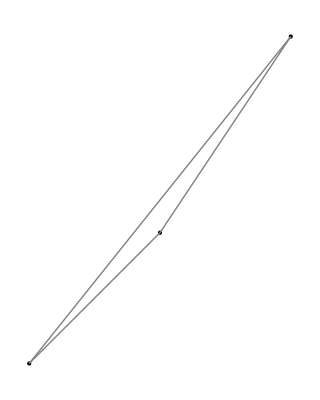

```mathematica
Stranice[{AA_,BB_,CC_}]:= {{AA,BB},{BB,CC},{CC,AA}}
Koti[{AA_,BB_,CC_}]:= {{CC,AA,BB},{AA,BB,CC},{BB,CC,AA}}
Koti[trikotnik]

SlikaOglisc[trikotnik_]:= Map[Point, trikotnik];
SlikaStranic[trikotnik_]:=Map[Line, Stranice[trikotnik]]
NarisiTrikotnik[trikotnik_]:=Graphics[
{PointSize[Large],
SlikaOglisc[trikotnik], 
{Gray,SlikaStranic[trikotnik]}
}, 
AspectRatio->Automatic]
NarisiTrikotnik[trikotnik]
```

```mathematica
DRUGA NALOGA
```

```mathematica
VektorSimetraleKota[{x_,y_,z_}] :=Normalize[Normalize[x-y]+Normalize[z-y]]

SimetralaKota[{x_,y_,z_}, dol_:10]:={y,y+VektorSimetraleKota[{x,y,z}]*dol}
```

TRETJA NALOGA

```mathematica
SlikaSimetralKotov[trikotnik_, dol_:10]:=Graphics[{Line[SimetralaKota[trikotnik,10]]}]
```

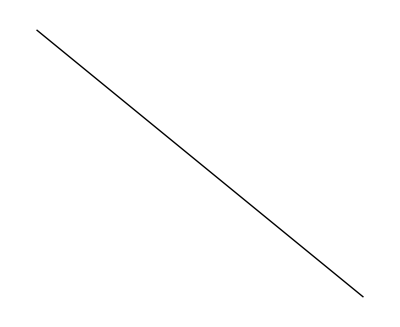

```mathematica
SlikaSimetralKotov[trikotnik]
```